# Mathematica Project - Machine Learning

## Introduction

In this project, we aim to use different functions present in Mathematica on a dataset that helps us train a system and identify any patterns in the data. We first pre-process the data with the objective of cleaning the data. Visualisation is performed on the cleaned data for better understanding of the data. Various state-of-the-art machine learning algorithms are applied to the data with the aim being classification of the data. The process is explained in detail in the coming section.

### Palmer Penguin data:

The Palmer penguins dataset consists of body measurements of three species of penguins found on three islands near Palmer Archipelago, Antarctica.  The dataset consists of 344 measurements or observations and 7 columns whose definitions are as follows:

species:  Denotes penguin species (Adélie, Chinstrap and Gentoo).
Island:  Denoting the island in which the observation was seen in Palmer Archipelago, Antarctica (Biscoe, Dream or Torgersen).
culmen_length_mm:  A numerical value that denotes the length of the upper ridge of a penguin’s bill (millimeters).
culmen_depth_mm: A numeric value denoting bill depth (millimeters).
flipper_length_mm: An integer value denoting flipper length (millimeters).
body_mass_g: An integer value denoting body mass (grams).
sex: Denotes the gender of the penguin(female, male).

#### Images of the three species of penguins :

```mathematica
LinguisticAssistant[{"Image","Name"}]
Entity["Species","Species:PygoscelisPapua"][{"Image","Name"}]
LinguisticAssistant[{"Image","Name"}]
```

{-Graphics-,Adelie penguin}

{-Graphics-,gentoo penguin}

{-Graphics-,chinstrap penguin}

We first start with the exploratory data analysis and visualizations to clean the data and also understand the distributions of the numerical attributes of the  data. We also try to see if there is a correlation between the numerical attributes of the data. After drawing a few conclusions and interpreting the data at hand we try and apply classification algorithms to predict the three species of the penguins.

## Exploratory Data Analysis

Importing a dataset:

SemanticImport was used rather than Import function because the Import function considers the column names in the first row of the dataset to be an observation instead of column names. We use missing data rules to replace NA’s in the data with Missing[] so that it is not considered as a string. For example, if we do not use Missing[] NA is considered as a string in the column sex instead of a blank or a missing value.  This can cause a problem when we are looking for columns that have empty values.

```mathematica
data=SemanticImport[NotebookDirectory[]<>"penguins.csv",MissingDataRules->{"NA"->Missing[]}];
```

Observing the first 5 observations to get a brief idea about the data

```mathematica
Take[data,5]
```

The dimensions show that we have 344 observations and 7 columns.

```mathematica
Dimensions[data]
```

{344,7}

Count the number of Missing values in each column

```mathematica
data[Count[_Missing],#]&/@ Keys@First@data
```

There are two missing values in each of the columns named culmen_length_mm, culmen_depth_mm, flipper_length_mm, body_mass_g. There are 10 missing values in the sex column.

For classification purposes we are just using the bodily measurements in the dataset to predict the species of the penguin. Hence, we just remove the rows that have missing values in the numerical columns and leave the column sex as it is . 
We first get the indices of the rows where the numerical data is missing.

```mathematica
Position[data[All,3;;6],_Missing]
```

{{4,Key[culmen_length_mm]},{4,Key[culmen_depth_mm]},{4,Key[flipper_length_mm]},{4,Key[body_mass_g]},{340,Key[culmen_length_mm]},{340,Key[culmen_depth_mm]},{340,Key[flipper_length_mm]},{340,Key[body_mass_g]}}

We can observe that the data is missing in the 4th and the 340th position hence we remove those observations from the data.

```mathematica
data=Delete[data,{{4},{340}}];
```

We observe that we have now removed our empty values in the data and the empty values in the gender column has been retained as it is.

```mathematica
data[1;;8]
```

Now we replace all the empty values in the gender column by the word “Unknown”

```mathematica
data= data[All,{"sex"->Replace[{_Missing->"Unknown"}]}];
data[1;;8]
```

## Visualizations

Having cleaned the data, we would now like to gain more insights on the data. Hence, we perform visualisations to interpret the data easily.

#### Distribution Types of the data:

Histograms were plotted to understand the distribution types of the numerical data present in the dataset.

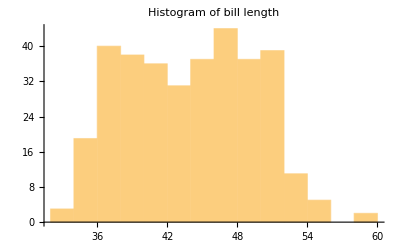

```mathematica
Histogram[data[All,"culmen_length_mm"],PlotLabel->"Histogram of bill length"]
```

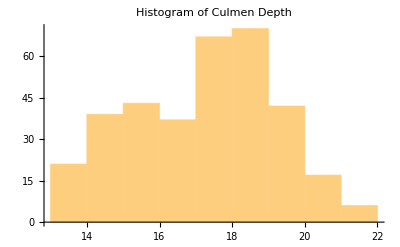

```mathematica
Histogram[data[All,"culmen_depth_mm"],PlotLabel->"Histogram of Culmen Depth"]
```

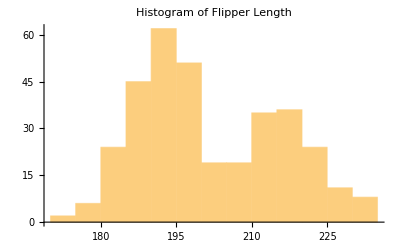

```mathematica
Histogram[data[All,"flipper_length_mm"],PlotLabel->"Histogram of Flipper Length"]
```

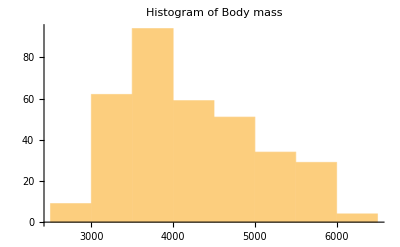

```mathematica
Histogram[data[All,"body_mass_g"],PlotLabel->"Histogram of Body mass"]
```

All the distributions look like that of a normal distribution hence there is no need of transforming any feature in the dataset.

Now we want to gain some general information about the data. Hence, we use some simple plots such as Bar-plots, Pie Charts and List Plots to gain some insights of the data.

### General Insights of the data:

We first would want to know the number of penguins belonging to each species so that we can decide if we are dealing with a class imbalance problem. Hence, a bar chart was plotted to understand this.

```mathematica
species=Normal[data[All,"species"]];
speciescount=Counts[species];
keys=Keys[speciescount];
```

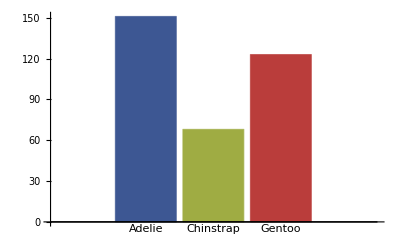

```mathematica
BarChart[speciescount,ChartLabels->keys,ChartStyle->"DarkRainbow"]
```

There is class - imbalance in chinstrap species but it might not cause a problem during classification because the samples are good enough for classification.

Next we would want to know how many females or male penguins are present in this data. Hence, a pie chart was plotted to understand if the data had equal number of male and female species.

```mathematica
gender=Normal[data[All,"sex"]];
gendercount=Counts[gender];
keys=Keys[gendercount];
PieChart[gendercount,ChartLabels->keys,ChartStyle->"DarkRainbow"]
```

-Graphics-

It was observed that the male and female populations are almost balanced and 9 samples are unknown.

A histogram was plotted to understand if each of the species had equal number of male and female species. It is evident from the graphs that the penguins that belonged to species Adelie has equal number of male and female species with 5 observations being unknown. Chinstrap penguins had equal number of male and female species as well  whereas Gentoo penguins had a slightly higher number of male species than female species with 4 observations belonging to unknown.

```mathematica
speciesbygender= data[All,{"species","sex"}];
speciesbygender = speciesbygender[All,{"sex"->Replace[{"FEMALE"->1,"MALE"->2,"Unknown"->3}]}];
speciesbygender[GroupBy["species"],Histogram,"sex"]
```

To gain a little more information on how the data was collected a histogram was plotted to understand if the observations of each species of the penguin was collected in different islands or not. We see that the observations from species Adelie has been collected from all the three islands whereas Chinstrap and Gentoo were collected from a single island (Torgersen or Biscoe or Dream).

```mathematica
islanddata= data[All,{"species","island"}];
islanddata =islanddata[All,{"island"->Replace[{"Torgersen"->1,"Biscoe"->2,"Dream"->3}]}];
islanddata[GroupBy["species"],Histogram,"island"]
```

#### Outlier Detection:

Next we plot box plots to see if there are any outliers in the data.

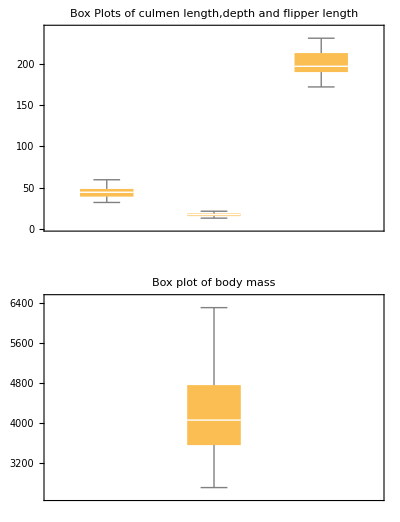

```mathematica
GraphicsColumn[{BoxWhiskerChart[{Normal[data[All,3]],Normal[data[All,4]],Normal[data[All,5]]},PlotLabel-> "Box Plots of culmen length,depth and flipper length"],BoxWhiskerChart[Normal[data[All,6]],PlotLabel->"Box plot of body mass"]}]
```

We see that there are no points lying outside the whiskers hence there are no outliers.

#### Feature Relation:

Since we want to use body measurements of the penguin to predict the type of species we see if there is any correlation between the numerical data.

We take the body measurement columns starting from index 3 to index 6 and form a correlation matrix. The first column and row corresponds to culmen_length_mm. The second column and row corresponds to culmen_depth_mm. The third column and row corresponds to flipper_length_mm. The last column and row corresponds to body_mass_g.

```mathematica
numericdata=Values[Normal[data[All,3;;6]]];
Correlation[numericdata]//MatrixForm
```

(1. | -0.235053 | 0.656181 | 0.59511
-0.235053 | 1. | -0.583851 | -0.471916
0.656181 | -0.583851 | 1. | 0.871202
0.59511 | -0.471916 | 0.871202 | 1.)

We see that culmen_length_mm has a positive correlation of 0.65 and 0.6 with flipper_length_mm and body_mass_g respectively.  We see a high correlation of 0.87 in between flipper_length_mm and body_mass_g. This means if the flipper_length increases then the body_mass also increases.

Culmen_depth_mm and flipper_length_mm are negatively correlated to each other. For plotting purposes we take only these observations since the rest of the correlations are weak.

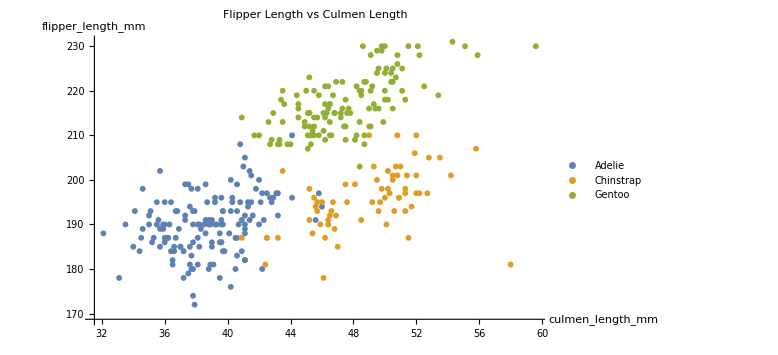

```mathematica
ListPlot[data[GroupBy[Key["species"]],All,{"culmen_length_mm","flipper_length_mm"}],PlotLegends->"Expressions",AxesLabel->Automatic,ImageSize->Large,PlotLabel->"Flipper Length vs Culmen Length"]
```

The penguins species Adelie has small culmen length and small flipper length. The Chinstrap species has a bigger culmen length as Adelie but the flipper length is the same as Adelie. Gentoo has a bigger bill length than Adelie  and almost the same bill length of Chinstrap species. However, the flipper length is higher than the other two species.

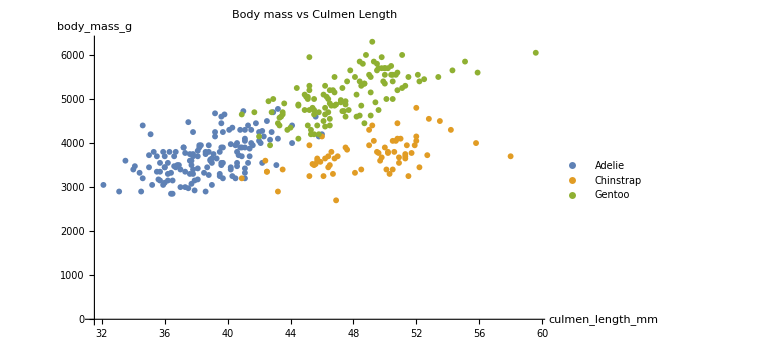

```mathematica
ListPlot[data[GroupBy[Key["species"]],All,{"culmen_length_mm","body_mass_g"}],PlotLegends->"Expressions",AxesLabel->Automatic,ImageSize->Large,PlotLabel->"Body mass vs Culmen Length"]
```

Chinstrap has higher culmen length as established previously but it has a lower body mass than the other species. Adelie has small culmen length however it has a slightly higher body mass than Chinstrap. Gentoo has high culmen length and high body mass.

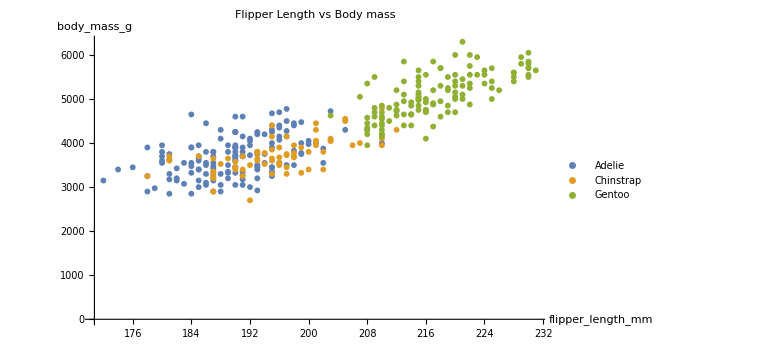

```mathematica
ListPlot[data[GroupBy[Key["species"]],All,{"flipper_length_mm","body_mass_g"}],PlotLegends->"Expressions",AxesLabel->Automatic,ImageSize->Large,PlotLabel->"Flipper Length vs Body mass"]
```

We can see a clear trend that as the flipper length increases the body mass starts increasing.

Having built the above insights from the data we now move on to classifying the data based on body measurements of the penguins

## Classification Models

Since we have multiple species, our classifying models should perform multi - label classification. The models that were built in this project were Naive Bayes Classifier, Random Forest, Nearest Neighbours, Neural Networks and Support Vector Machines with the aim of building a classifier that is the best fit for the data and improving the accuracy.

Since we have all the species grouped together, it is not fair to divide the data into test and train data. Hence, we shuffle the data and then split them to train and test data.

```mathematica
data=RandomSample[data];
Take[data,5] (*Looking at a few observations to check if the data has been shuffled*)
```

Now we transform the data into associations such hat it can be used in the Classify[] function. We pair the numerical values available from the indices 3 to 6 with the name of the species. A simple demonstration is given in the following piece of code.

```mathematica
ToString[data[1][[1]]]->Values[Normal[data[1][[3;;6]]]]
```

Adelie→{41.5,18.5,201,4000}

We implement the above code to iterate over the data and split the first half of the data to train and the rest to test data.

```mathematica
trainingData=GroupBy[Table[ToString[data[i][[1]]]->Values[Normal[data[i][[3;;6]]]],{i,1,Length[data]/2}],First->Last];
testingData=GroupBy[Table[ToString[data[i][[1]]]->Values[Normal[data[i][[3;;6]]]],{i,Length[data]/2+1,Length[data]}],First->Last];
```

### Naive Bayes Classifier:

The naive Bayes classifier is used for classification purposes but it assumes that each observation is independent of each other .

Train the model:

```mathematica
nb=Classify[trainingData,Method->"NaiveBayes"] (*Training data is used to train the model*)
```

ClassifierFunction[…]

A small description of how the Naive Bayes classifier works .

```mathematica
Information[nb,"MethodDescription"]
```

The naive Bayes classifier assumes that features are generated independently given the class and uses Bayes' theorem to predict the class.

Information[] gives information of the classifier built. It shows us the learning curve and performance measure of the classifier on the training data. Here, we have training accuracy of 90%.

```mathematica
Information[nb]
```

Classifier information
Data type | Mixed (number: 4)
Classes | ,,AdelieChinstrapGentoo
Accuracy | (90.5.) %
Method | NaiveBayes
Single evaluation time | 4.15 ms/example
Batch evaluation speed | 28.9 examples/ms
Loss | 0.328 ± 0.11
Model memory | 163. kB
Training examples used | 171 examples
Training time | 417. ms
 |

The trained model is used to make predictions on the test data. The test accuracy is around 94%. After running the code for multiple times sometimes  the test accuracy is more than train accuracy and hence it could be slightly overfitting the data.

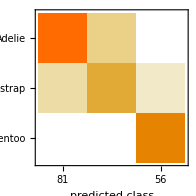
Classifier Measurements
Classifier method | NaiveBayes
Number of test examples | 171
Accuracy | (94.71.7) %
Accuracy baseline | (49.4.) %
Geometric mean of probabilities | 0.895 ± 0.024
Mean cross entropy | 0.11 ± 0.027
Single evaluation time | 4.84 ms/example
Batch evaluation speed | 9.9 examples/ms
-Graphics- |

```mathematica
measurenb=ClassifierMeasurements[nb,testingData]
```

A confusion matrix is plotted to show how many of them were correctly predicted and how many of them were misclassified. Since we have a class-imbalance problem it is better to look at the F-score then the accuracy.

```mathematica
measurenb/@{"FScore"} //TableForm
```

<|Adelie→0.95122,Chinstrap→0.865672,Gentoo→0.990991|>

The F measures tell that Gentoo is predicted accurately 99 % of the time, Adelie is predicted accurately 89% of the time and Chinstrap is predicted accurately 76% of the time.

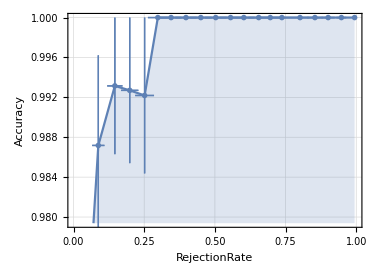

```mathematica
Show[measurenb["AccuracyRejectionPlot"],ImageSize->{377,269},AspectRatio->Full]
```

### RandomForest :

The random forest is used for classification purposes and creates multiple number of decision trees which are trained on a subset of variables instead of the whole dataset itself.

Train the model :

```mathematica
rf=Classify[trainingData,Method->"RandomForest"]
```

ClassifierFunction[…]

```mathematica
Information[rf,"MethodDescription"]
```

The random forest classifier uses an ensemble of decision trees to predict the class. Each decision tree has been trained on a random subset of the training set, and only uses a random subset of the features.

The training accuracy is approximately around 90%

```mathematica
Information[rf]
```

Classifier information
Data type | Mixed (number: 4)
Classes | ,,AdelieChinstrapGentoo
Accuracy | (90.02.6) %
Method | RandomForest
Single evaluation time | 4.73 ms/example
Batch evaluation speed | 33.4 examples/ms
Loss | 0.349 ± 0.04
Model memory | 238. kB
Training examples used | 171 examples
Training time | 598. ms
 |

We predict the classes of the test data based on the trained model. We see that the test accuracy is around 97% approximately. When the algorithm is run for multiple times by shuffling the data we observe that the test accuracy is more than that of training.  Hence even random Forest could be overfitting in some cases.

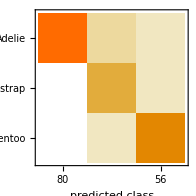
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 171
Accuracy | (97.11.3) %
Accuracy baseline | (49.4.) %
Geometric mean of probabilities | 0.908 ± 0.028
Mean cross entropy | 0.097 ± 0.031
Single evaluation time | 5.73 ms/example
Batch evaluation speed | 8.84 examples/ms
-Graphics- |

```mathematica
measurerf=ClassifierMeasurements[rf,testingData]
```

```mathematica
measurerf/@{"FScore"} //TableForm
```

<|Adelie→0.981595,Chinstrap→0.941176,Gentoo→0.972973|>

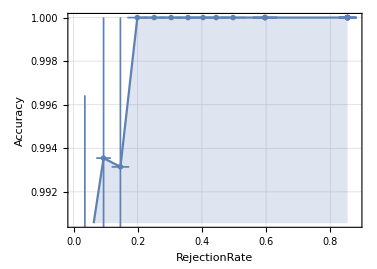

```mathematica
Show[measurerf["AccuracyRejectionPlot"],ImageSize->{377,269},AspectRatio->Full]
```

As far as accuracy of predicting is considered Random Forest performs better than the Naive Bayes classifier.

### Nearest Neighbours :

It is commonly called the k nearest neighbours where the class of an observation is predicted based on the majority of the class the neighbouring observations belong to.

Train the model :

```mathematica
nn=Classify[trainingData,Method->"NearestNeighbors"]
```

ClassifierFunction[…]

```mathematica
Information[nn,"MethodDescription"]
```

The nearest neighbors predictor predicts the value of a new example by analyzing its nearest neighbors in the feature space. In its simplest form, it averages the values of the "k"-nearest neighbors.

The training accuracy is around 94 % approximately .

```mathematica
ClassifierInformation[nn]
```

Classifier information
Data type | Mixed (number: 4)
Classes | ,,AdelieChinstrapGentoo
Accuracy | (94.71.8) %
Method | NearestNeighbors
Single evaluation time | 3.22 ms/example
Batch evaluation speed | 68.4 examples/ms
Loss | 0.195 ± 0.03
Model memory | 148. kB
Training examples used | 171 examples
Training time | 416. ms
 |

The test accuracy is 99.4 % approximately. However, it seems that the model is overfitting because the train accuracy is more than that of the test accuracy. From the confusion matrix, we observe that the species belonging to Gentoo is being predicted accurately.

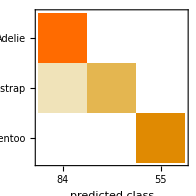
Classifier Measurements
Classifier method | NearestNeighbors
Number of test examples | 171
Accuracy | (99.40.6) %
Accuracy baseline | (49.4.) %
Geometric mean of probabilities | 0.94 ± 0.0071
Mean cross entropy | 0.062 ± 0.0076
Single evaluation time | 3.31 ms/example
Batch evaluation speed | 13.3 examples/ms
-Graphics- |

```mathematica
measurenn=ClassifierMeasurements[nn,testingData]
```

The Fscore also hints at the fact that this model performs better than the Naive Bayes and Random Forest at generalizing the data.

```mathematica
measurenn/@{"FScore"} //TableForm
```

<|Adelie→0.994012,Chinstrap→0.984615,Gentoo→1.|>

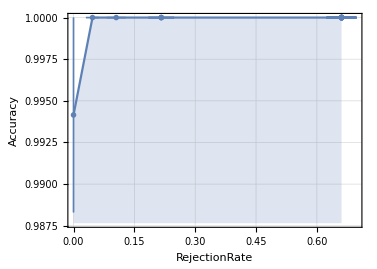

```mathematica
Show[measurenn["AccuracyRejectionPlot"],ImageSize->{377,269},AspectRatio->Full]
```

### Neural Network :

A neural network is a complex network that has many layers in which there are a number of units called neurons. Every layer tries to capture the data and learn something from the data which is the input to the next layer.

```mathematica
nnet=Classify[trainingData,Method->"NeuralNetwork"]
```

ClassifierFunction[…]

```mathematica
Information[nnet,"MethodDescription"]
```

An neural networks is composed of layers of artificial neuron units. Each 
unit computes its value as a function of the unit values in the previous layer. Information 
is processed layer by layer from the feature layer to the output layer which gives the class probabilities. It is 
also called a feed-forward neural network or a multi-layer perceptron.

The training accuracy is around 98%.

```mathematica
ClassifierInformation[nnet]
```

Classifier information
Data type | Mixed (number: 4)
Classes | ,,AdelieChinstrapGentoo
Accuracy | (98.01.7) %
Method | NeuralNetwork
Single evaluation time | 3.29 ms/example
Batch evaluation speed | 51.8 examples/ms
Loss | 0.0491 ± 0.029
Model memory | 400. kB
Training examples used | 171 examples
Training time | 14.8 s
 |

The test accuracy is around 98.5% approximately which is slightly overfitting. The confusion matrix says that the species Gentoo is accurately predicted here too. Neural Networks seems like the best fit for the data when compared to the other models we have built now.

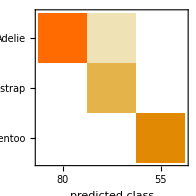
Classifier Measurements
Classifier method | NeuralNetwork
Number of test examples | 171
Accuracy | (98.21.0) %
Accuracy baseline | (49.4.) %
Geometric mean of probabilities | 0.962 ± 0.022
Mean cross entropy | 0.0383 ± 0.023
Single evaluation time | 3.58 ms/example
Batch evaluation speed | 8.92 examples/ms
-Graphics- |

```mathematica
measurennet=ClassifierMeasurements[nnet,testingData]
```

```mathematica
measurennet/@{"FScore"} //TableForm
```

<|Adelie→0.981595,Chinstrap→0.956522,Gentoo→1.|>

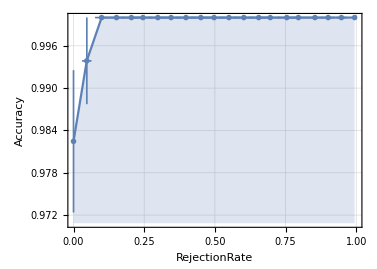

```mathematica
Show[measurennet["AccuracyRejectionPlot"],ImageSize->{377,269},AspectRatio->Full]
```

### Support Vector Machine :

In the SVM algorithm, we plot each observation as a point in n - dimensional space (where n is the number of features in this case 4) . We then perform our classification by finding a hyperplane that differentiates between the classes .

```mathematica
svm=Classify[trainingData,Method->"SupportVectorMachine"]
```

ClassifierFunction[…]

```mathematica
Information[svm,"MethodDescription"]
```

The support vector machine classifier separates the training data into two classes using a 
			maximum-margin hyperplane. The original feature space can be mapped into a higher dimensional space to 
			improve linear separability. The multi-class classification problem is reduced to a set of binary 
			classification problems.

The training accuracy seen here is around 95 %.

```mathematica
Information[svm]
```

Classifier information
Data type | Mixed (number: 4)
Classes | ,,AdelieChinstrapGentoo
Accuracy | (98.11.6) %
Method | SupportVectorMachine
Single evaluation time | 4.67 ms/example
Batch evaluation speed | 30.8 examples/ms
Loss | 0.101 ± 0.039
Model memory | 262. kB
Training examples used | 171 examples
Training time | 3.24 s
 |

The test accuracy is 98.8 % which also makes SVM the best fit for the data at hand. The confusion matrix says that the species Gentoo is accurately predicted.

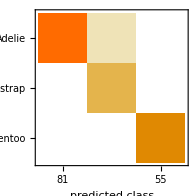
Classifier Measurements
Classifier method | SupportVectorMachine
Number of test examples | 171
Accuracy | (98.80.8) %
Accuracy baseline | (49.4.) %
Geometric mean of probabilities | 0.965 ± 0.024
Mean cross entropy | 0.0359 ± 0.025
Single evaluation time | 5.85 ms/example
Batch evaluation speed | 7.93 examples/ms
-Graphics- |

```mathematica
measuresvm=ClassifierMeasurements[svm,testingData]
```

```mathematica
measuresvm/@{"FScore"} //TableForm
```

<|Adelie→0.987805,Chinstrap→0.970588,Gentoo→1.|>

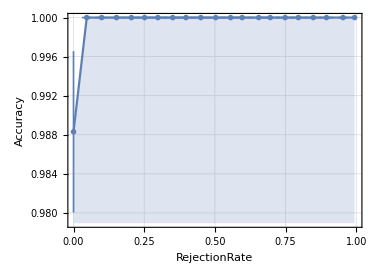

```mathematica
Show[measuresvm["AccuracyRejectionPlot"],ImageSize->{377,269},AspectRatio->Full]
```

Conclusion :

SVM and Neural Networks work well for the data giving us an accuracy of 98.5 % on an average. However, when the code of neural networks was run for multiple times on different subsets of data obtained by shuffling, it was observed that sometimes neural networks was overfitting for the data. Therefore, given any type of data regardless of shuffling SVM seems to be performing well than Neural Networks without overfitting the data. The algorithm is able to classify observations belonging to Gentoo correctly but there seems to be a slight confusion in classifying species belonging to Adelie and Chinstrap.